# Learning MNIST

```mathematica
Get["neural-logic.m",Path->SetDirectory[ParentDirectory[NotebookDirectory[]]<>"/prototype"]]
```

## Get data

```mathematica
data=ResourceData["MNIST"];
examples=[Binarize[First[#]]->Last[#]&,data];
effectiveExamples=examples;
```

```mathematica
smallExamples=[ImageResize[First[#],{8,8}]->Last[#]&,examples];
first4Digits=24754;
effectiveExamples=Take[smallExamples,first4Digits];
```

```mathematica
inputSize=Fold[Times,1,ImageDimensions[First[First[effectiveExamples]]]];
classes=DeleteDuplicates[Last/@effectiveExamples];
```

```mathematica
{trainData,testData}=[effectiveExamples,"TestSetSize"->Scaled[0.2],"Shuffle"->True];
Take[trainData,20]
```

{-Graphics-→2,-Graphics-→0,-Graphics-→1,-Graphics-→2,-Graphics-→2,-Graphics-→0,-Graphics-→0,-Graphics-→2,-Graphics-→1,-Graphics-→0,-Graphics-→3,-Graphics-→3,-Graphics-→0,-Graphics-→0,-Graphics-→3,-Graphics-→1,-Graphics-→1,-Graphics-→3,-Graphics-→2,-Graphics-→2}

## Create feature encoders

```mathematica
inputEncoder=NetEncoder[{"Function",Flatten[ImageData[#]]&,{inputSize}}];
targetEncoder=NetEncoder[{"Class",classes,"IndicatorVector"}];
```

## Create net

```mathematica
{net,hardNet}=With[{classificationLayerSize=32*Length[classes]},
HardNeuralChain[{
HardNeuralNAND[inputSize,128],
HardNeuralAND[128,classificationLayerSize],
HardNeuralReshapeLayer[classificationLayerSize,Length[classes]]
}]];
```

```mathematica
trainableNet=NetGraph[
<|"Net"->net,"Loss"->HardClassificationLoss[]|>,
{"Net"->"Loss"},"Input"->inputEncoder,"Target"->targetEncoder
];
```

## Train net

```mathematica
result=NetTrain[trainableNet,trainData,All,
ValidationSet->testData,
LossFunction->"Loss",
Method->{"ADAM"},
TargetDevice->"GPU",
MaxTrainingRounds->20000];
```

## Evaluate soft net

```mathematica
{trainedSoftNet,trainedHardNet}=NetGraph[
<|"TrainedNet"->NetDelete[NetFlatten[#],"Loss/Error"]|>,
{},"Output"->NetDecoder[targetEncoder]
]&/@{result["TrainedNet"],HardenNet[result["TrainedNet"]]};
```

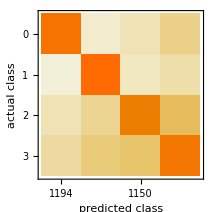
{Classifier Measurements
Classifier method | Net
Number of test examples | 4951
Accuracy | (91.60.4) %
Accuracy baseline | (25.90.6) %
Geometric mean of probabilities | 0.777 ± 0.0091
Mean cross entropy | 0.253 ± 0.012
Single evaluation time | 4.44 ms/example
Batch evaluation speed | 3.84 examples/ms
-Graphics- | ,Classifier Measurements
Classifier method | Net
Number of test examples | 4951
Accuracy | (91.60.4) %
Accuracy baseline | (25.90.6) %
Geometric mean of probabilities | 0.777 ± 0.0091
Mean cross entropy | 0.253 ± 0.012
Single evaluation time | 4.63 ms/example
Batch evaluation speed | 3.75 examples/ms
-Graphics- | }

```mathematica
ClassifierMeasurements[#,testData]&/@{trainedSoftNet,trainedHardNet}
```

## Evaluate hard net

```mathematica
hnf=HardNetFunction[hardNet,trainedHardNet];
```

```mathematica
hncwt=HardNetClassify[hnf,testData,NetDecoder[targetEncoder],inputEncoder[First[#]]&,Last[#]&];
```

```mathematica
eval=HardNetClassifyEvaluation[hncwt];
eval["Accuracy"]
```

0.912745

```mathematica
hncwt2=[Association[{"Prediction"->trainedHardNet[First[#]],"Target"->Last[#]}]&,testData];
```

```mathematica
eval2=HardNetClassifyEvaluation[hncwt2];
eval2["Accuracy"]
```

0.912745

```mathematica
Quantity[Length[Flatten[ExtractWeights[trainedSoftNet]]]/8/1024//N,"Kilobytes"]
```

3.01563 kB

```mathematica
HardNetBooleanExpression[hnf,inputSize];
```

## Standard net

```mathematica
net=With[{classificationLayerSize=numClasses},
NetChain[{
300,LogisticSigmoid,
classificationLayerSize,LogisticSigmoid,
SoftmaxLayer[]
},
"Output"->NetDecoder[{"Class",{"0","1","2","3"}}]
]];
```